Socio-Climate model - Simple (Bauch)

## Setup

```mathematica
SetDirectory["/Users/tbury/Library/Mobile Documents/com~apple~CloudDocs/Research/climate_social"];
```

```mathematica
(* Good fonts *)
TMBFS10={FontFamily->"Helvetica",FontSize->10};
TMBFS12={FontFamily->"Helvetica",FontSize->12};
TMBFS15={FontFamily->"Helvetica",FontSize->15};
TMBbold={FontFamily->"Helvetica",FontSize->15,Bold};
(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

## Parameters and Dynamics

```mathematica
(* Clear function names *)
Clear[f,g,u,res]
(* Clear state variables *)
Clear[car,x]
(* Clear parameter values *)
Clear[ϵ,κ,β,γ,δ,umax,ω,b,c,d,σ1,σ2];
```

```mathematica
(* Physical values *)
ϵ=0.01;
umax=10;
γ=1*10^-4;
ω=1*10^-3;

(* social values *)
κ=0.05;
β=1;
δ=1;


(* response function parameters F(T) *)
resType=1; (* 1 linear, 2 logistic, 3 cubic *)
fmax=4;
b1=fmax/umax;
c1=0;

b2=2fmax;
c2=1;
d2=0.5;

b3=(umax^3/fmax)^(1/3);
c3=0;

(* noise amplitudes *)
σ1=0.01;
σ2=0.01;

(* simulation parameters *)
dt=0.25; (* time step for stochastic simulation *)
tmax=100; (* max time (simulation stop) *)
seed=1; (* seed number *)
numSims=2;(* number of simulations *)
{car0,x0}={1000,0.01}; (* initial condition *)
```

```mathematica
(* dispaly parameters *)
{b1,c1,b2,c2,d2,b3,c3}//N
```

{0.4,0.,8.,1.,0.5,6.29961,0.}

### Cost of global warming function

```mathematica
(* social response to temperature function *)
Clear[resLin,resLog,resCub,res]
resLin[u_]:=b1 u + c1;
resLog[u_]:=b2/(1+c2 Exp[-d2 u])-fmax;
resCub[u_]:=(u/b3)^3+c3;
Which[resType==1,res[u_]:=resLin[u],
resType=2,res[u]:=resLog[u],
resType=3,res[u]:=resCub[u]]
```

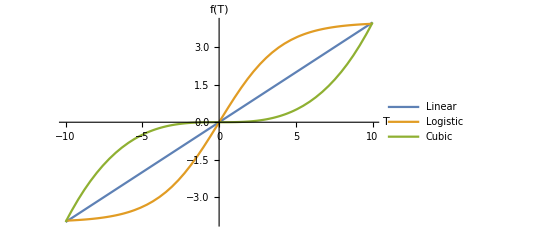

```mathematica
(* Make plot of three functions *)
warmCostPlot=Plot[{resLin[u],resLog[u],resCub[u]},{u,-umax,umax},
LabelStyle->14,
AxesLabel->{"T","f(T)"},
PlotLegends->{"Linear","Logistic","Cubic"}]
```

```mathematica
Export["figures/warmCostPlot.png",warmCostPlot];
```

### Temperature function

```mathematica
(* Temperature relation *)
u[c_]:=-umax+2umax/(1+Exp[-ω c]);
```

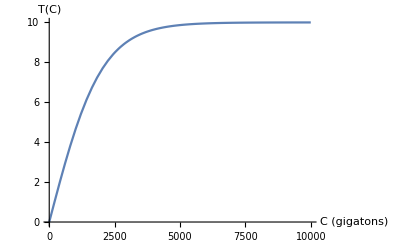

```mathematica
tempPlot=Plot[u[c],{c,0,10000},PlotRange->All,
LabelStyle->14,
AxesLabel->{"C (gigatons)","T(C)"}]
```

```mathematica
Export["figures/tempPlot.png",tempPlot];
```

### DE functions

```mathematica
(* Dynamic equations for C and x *)
f[car_,x_]:=ϵ(1-x)-γ car;
g[car_,x_]:=κ x(1-x)(-β+res[u[car]]+δ (2x-1))
```

## Simulation

```mathematica
(* clear function labels *)
Clear[stochProc,stochSol,stochData]
```

```mathematica
(* define the stocahstic process *)
stochProc[{car0_,x0_},{a1_,a2_}]:=ItoProcess[{ⅆcar[t]==(f[car[t],x[t]])ⅆt + σ1 car[t] ⅆw1[t],
ⅆx[t]==(g[car[t],x[t]])ⅆt + σ2 ⅆw2[t]},
{car[t],x[t]},{{car,x},{car0,x0}},t,{w1\[Distributed]WienerProcess[],w2\[Distributed]WienerProcess[]}]
```

```mathematica
(* define simulation *)
SeedRandom[seed];
stochSol[{car0_,x0_},{σ1_,σ2_}]:=RandomFunction[stochProc[{car0,x0},{σ1,σ2}],{0,tmax,dt},numSims,Method->"EulerMaruyama"]
```

```mathematica
(* run simulation to obtain data *)
stochData=stochSol[{c0,x0},{σ1,σ2}];
```

```mathematica
pathData=stochData["Paths"];
pathData//Dimensions
```

{2,401,2}

```mathematica
(* extract time series data *)
tVals=pathData[[1,;;,1]];
carVals=pathData[[;;,;;,2,1]];
uVals=u[carVals];
xVals=pathData[[;;,;;,2,2]];
```

## Plots

```mathematica
(* carbon plot *)
carPlot=ListLinePlot[{Transpose[{tVals,carVals[[1]]}]},
PlotRange->{0,1200}];
```

```mathematica
(* Temperature plot *)
tempPlot=ListLinePlot[{Transpose[{tVals,uVals[[1]]}]},
PlotRange->{0,2umax}];
```

```mathematica
(* mitigators plot *)
mitPlot=ListLinePlot[{Transpose[{tVals,xVals[[1]]}]},
PlotRange->All];
```

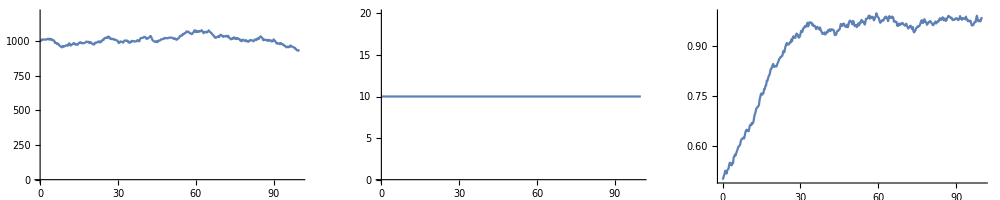

```mathematica
GraphicsRow[{carPlot,tempPlot,mitPlot},ImageSize->1000]
```